

```mathematica
Graphics[Circle[]]
```



```mathematica
Graphics[Disk[]]
```

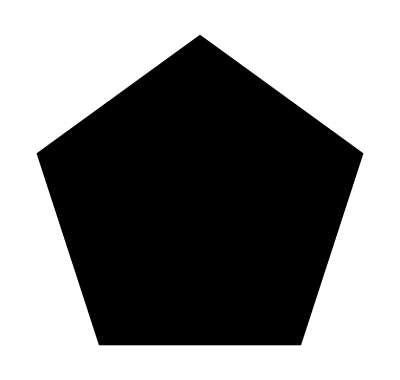

```mathematica
Graphics[RegularPolygon[5]]
```

Vocabulary

```mathematica
Graphics expressions: 
Graphics[]
```

Graphics (expressions:-Graphics-)

```mathematica
Graphics3D[]
```

-Graphics3D-

Graphics promitives

```mathematica
Circle[]
```

Circle[{0,0}]

```mathematica
Disk[]
```

Disk[{0,0}]

```mathematica
Sphere[]
```

Sphere[{0,0,0}]

```mathematica
Graphics3D[Sphere[]]
```

-Graphics3D-

```mathematica
Graphics3D[Cone[]]
```

-Graphics3D-

So far:
	- can draw individual geometical elements (graphics promitives): 개별 지오메트리 요소를 그릴 수 있습니다(각종 프로모티브).
    Still needed:
    	- ability to combine geometical elements:기하학적 요소를 결합할 수 있는 능력
        	- ability to control appearance (coloe, thickness, etc.): 외형 조절 능력(채색, 두께 등)
            	- ability to move things around: 물건을 움직이는 능력

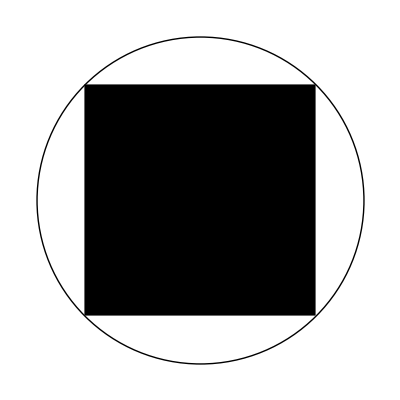

```mathematica
Graphics[{RegularPolygon[4], Circle[]}]
```

```mathematica
Graphics[{Style[RegularPolygon[4], Red], Circle[]}]
```

-Graphics-

```mathematica
Graphics[{Style[RegularPolygon[4], Red],Style[ Circle[], Thickness[0.2]] }]
```

-Graphics-

```mathematica
Graphics[{Style[RegularPolygon[4], Red], Style[Circle[], Thickness[0.2], Opacity[0.5]]}]
```

-Graphics-

Vocabulary
	Graphics expressions: Graphics[...], Graphics3D[...], ...
    	Graphics primitives: Circle[], Disk[], Sphere[]
        	Graphics directives: Red, Thickness[0.2], Opacity[0.5], ...

```mathematica
Graphics[RegularPolygon[5]]
```

-Graphics-

```mathematica
Graphics[Style[RegularPolygon[5], Orange]]
```

-Graphics-

```mathematica
Table[RegularPolygon[n], {n,3,6}]
```

{RegularPolygon[3],RegularPolygon[4],RegularPolygon[5],RegularPolygon[6]}

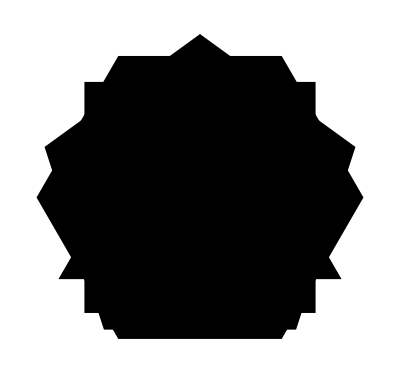

```mathematica
Graphics[Table[Style[RegularPolygon[n], Opacity[0.2]], {n,3,6}]]
```

Vocabulary
	Graphics[...]
    	Graphics3D[...]
        Graphics primitives:
        	Circle[], Disk[], RegularPolygon[5], ...
            	Sphere[], Cylinder[], Cone[], ...
        Graphics directives:
        	Style[Circle[], Red]
            	Red, Orange, Thickness[0.2], Opacity[0.5], ...

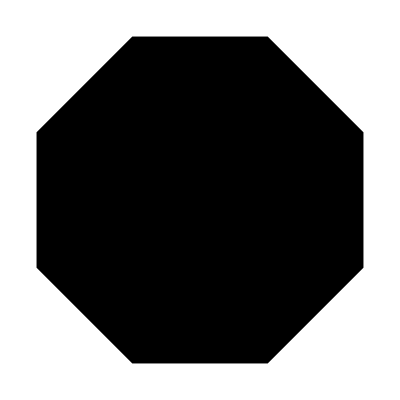

```mathematica
Graphics[Style[RegularPolygon[8], Red]]
```

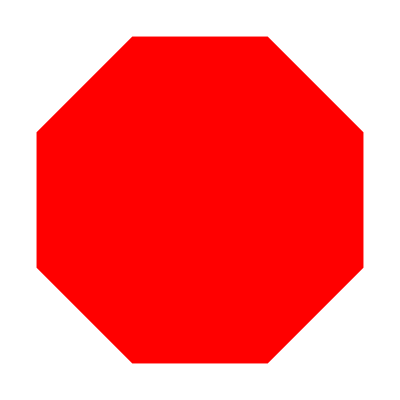

```mathematica
Graphics[{Red,RegularPolygon[8]}]
```